# Quantum Arithmetic

We will cover quantum arithmetic circuits centered on the Quantum Fourier Transform, showing how QFT enables addition and multiplication, how these operations are implemented in the Fourier basis, and how to transform to and from that basis.

## Key Concepts

Quantum Fourier Transform

Phase Basis

## The Discrete Fourier Transform

The discrete Fourier transform is a mathematical transformation that is very useful in processing data. It has many applications and is often employed when one wants to analyze signals over time.

This transformation on a list of n numbers is given by the so-called Fourier matrix of size n. For example, the Fourier matrix of size 4 looks like:

```mathematica
FourierMatrix[4]//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | ⅈ/2 | -1/2 | -ⅈ/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -ⅈ/2 | -1/2 | ⅈ/2)

Recall that quantum states of n qubits can be represented by a list of 2^n complex amplitudes. For example, 8 complex amplitudes describe 3 qubits:

```mathematica
QuantumState["RandomPure"[3]]["StateVector"]//MatrixForm
```

(-0.230866+0.0284542 ⅈ
-0.110406+0.351639 ⅈ
-0.254187+0.0650864 ⅈ
0.48689+0.244406 ⅈ
0.0220076-0.286277 ⅈ
0.478707+0.22564 ⅈ
-0.193727-0.201168 ⅈ
-0.0058361-0.0621525 ⅈ)

The most naive way to implement the classical discrete fourier transform on a list of 2^n complex data points requires O(2^(2n)) operations. However, there are other methods known as Fast Fourier Transforms. These faster methods only require O(n 2^n) classical operations. Because 2^n complex data points can be encoded in only n qubits, the quantum Fourier transform requires only O(n^2) quantum gates to be applied to these n qubits.

The Quantum Fourier Transform maps an n-qubit computational-basis state to a uniform superposition whose phases encode the original index in Fourier order:

QFTx=1/(√(2^n))∑_(y=0)^(2^n-1) ⅇ^(2π ⅈ xy/2^n)y with 0<=x<=2^n-1

QFT is a basis change. For a general 2-qubit state with four amplitudes (ordered as 00, 01, 10, 11), the 2-qubit QFT applies a 4-point discrete Fourier transform to those amplitudes. In words: each basis component spreads over all four outputs with specific relative phases; the new four amplitudes are the Discrete Fourier Transform of the original four.

```mathematica
MatrixForm[Array[Subscript[c, ##]&,2^2]]->MatrixForm@FullSimplify@Normal@QuantumCircuitOperator["Fourier"[2]][QuantumState[Array[Subscript[c, ##]&,2^2]]]["StateVector"]
```

(c_1
c_2
c_3
c_4)→(1/2 (c_1+c_2+c_3+c_4)
1/2 (c_1+ⅈ (c_2+ⅈ c_3-c_4))
1/2 (c_1-c_2+c_3-c_4)
1/2 (c_1-ⅈ c_2-c_3+ⅈ c_4))

Of course, you can also implement this directly with matrix operations on the state vector:

```mathematica
MatrixForm@FullSimplify[FourierMatrix[4].Array[Subscript[c, ##]&,2^2]]
```

(1/2 (c_1+c_2+c_3+c_4)
1/2 (c_1+ⅈ (c_2+ⅈ c_3-c_4))
1/2 (c_1-c_2+c_3-c_4)
1/2 (c_1-ⅈ c_2-c_3+ⅈ c_4))

The circuit to implement a 3-qubit QFT is given below:

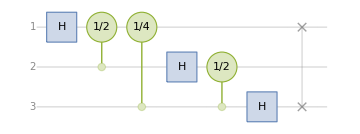

```mathematica
QuantumCircuitOperator["Fourier"[3]]["Diagram"]
```

Note the SWAP operation at the end; these are present so that the operator’s matrix elements are identical to the Fourier matrix of the appropriate size. Depending on the conventions for encoding the classical information, the SWAP operations may or may not appear in other texts.

```mathematica
QuantumCircuitOperator["Fourier"[3]]["Matrix"]==FourierMatrix[2^3]
```

True

Transforming a quantum state into the Fourier basis is exactly the action of the QFT on that state. Think of the QFT as the basis change to the Fourier basis.

## Phase Basis Encoding

As we discussed before, the computational basis is not the only way to encode classical information in a quantum state. Recall that the relative phase between two states can be experimentally distinguished. Thus, even if two states have the same probability to obtain outcomes in the computational basis, they are not the same state and will give different probabilities for outcomes in some other basis.

With this in mind, consider the following circuit:

```mathematica
QuantumCircuitOperator["PhaseNumber"[1,3]]["Diagram",ImageSize->100]
```

-Graphics-

In the above circuit, green circles represent “PhaseShift” gate, which is a phase gate with the angle π/2^(n-1). The corresponding label is 1/2^(n-1). It means the label 1/4 means a phase of π/4.

The above circuit encodes an integer in n qubits. Here, the integer 1 is encoded in three qubits. In 3-bit binary, 1 is 001.

```mathematica
IntegerDigits[1,2,3]
```

{0,0,1}

But how do you "read out" this phase information if all the measurements are performed in the computational basis? If you simply try to measure, the information encoded in the qubit phases is lost.

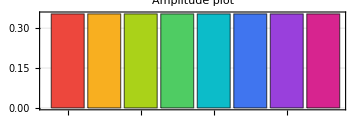

```mathematica
QuantumCircuitOperator["PhaseNumber"[1,3]][]["AmplitudesChart",]
```

As you can see from the changing colors in the above plot, the information of the input state is transferred to information about the relative phases of each qubit (with respect to a uniform superposition in the computational basis). But that information is not accessible if measuring in the computational basis:

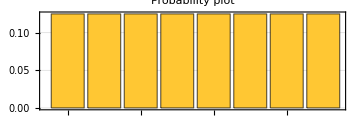

```mathematica
QuantumCircuitOperator["PhaseNumber"[1,3]][]["ProbabilitiesPlot",]
```

As you can see from the plot, the phase information is not immediately accessible in the computational basis. Instead, you must perform the inverse of the quantum fourier transform, and then measure.

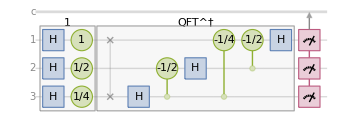

```mathematica
QuantumCircuitOperator[{"PhaseNumber"[1,3],"InverseFourier"[3],"M"->Range[3]}]["Diagram"]
```

By performing the inverse quantum Fourier transform, all of the phase information is now encoded in the computational basis. The measurement outcome is now the same as the number which was encoded in the phase basis:

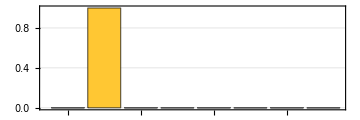

```mathematica
QuantumCircuitOperator[{"PhaseNumber"[1,3],"InverseFourier"[3],"M"->Range[3]}][]["ProbabilitiesPlot",]
```

With the phase basis and QFT in hand, you can implement quantum arithmetic circuits. The final state 001 matches the 3-qubit binary encoding of the integer 1.

## Quantum Phase Adders

Let’s say you want to build a circuit which adds three to your input. The input state is a bit-string state such as 1100 for 12. As with any digital computation, the arithmetic is performed mod 2^n, where n is the number of qubits used.

Let’s use this to compute 12+3 using four qubits. Find the integer string of 12 in the base-2:

```mathematica
IntegerString[12,2,4]
```

1100

Build the circuit as follows: prepare the 4-qubit register in 12, apply the QFT to transform it into the Fourier basis, perform addition of 3 in the Fourier basis using PhaseNumber circuit but without Hadamard, then apply the inverse QFT to return to the computational basis. The final state is 15 (mod 2^4).

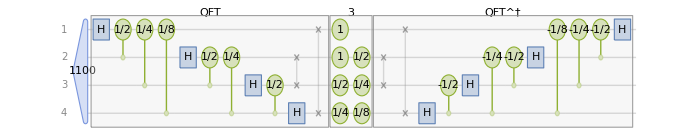

```mathematica
QuantumCircuitOperator[{"1100","Fourier"[4],"PhaseNumber"[3,4,False],"InverseFourier"[4]}]["Diagram",ImageSize->700]
```

This circuit first performs a quantum Fourier transform to get the input information into the phase basis, then applies an operation to add 3 in the phase basis, then performs an inverse quantum Fourier transform, and finally measures the results:

Find the measurement probabilities:

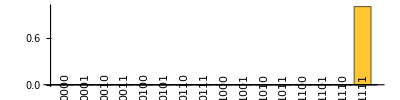

```mathematica
QuantumCircuitOperator[{"1100","Fourier"[4],"PhaseNumber"[3,4,False],"InverseFourier"[4]}][]["ProbabilitiesPlot",]
```

Given the outcome with maximum probability, determine the corresponding integer (using the bitstring-to-integer mapping):

```mathematica
FromDigits["1111",2]
```

15

With probability 1, this circuit gives the state corresponding to 15, the correct result for 12+3.

It is possible for the input to be a superposition of states. For example, suppose you didn’t know whether you wanted your input to be 6 or 4. You can run both computations at the same time using the previous type of circuit:

```mathematica
ψInputSuperposition=QuantumState[QuantumState["0110"]+QuantumState["0100"],"Label"->"6+4"]["Normalize"];
ψInputSuperposition["Formula"]
```

1/(√2)0100+1/(√2)0110

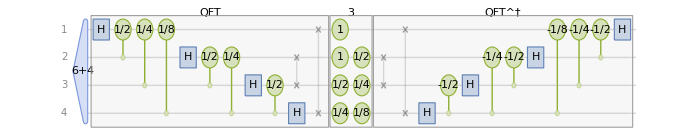

```mathematica
QuantumCircuitOperator[{ψInputSuperposition,"Fourier"[4],"PhaseNumber"[3,4,False],"InverseFourier"[4]}]["Diagram",ImageSize->700]
```

Since the input was a superposition of states corresponding to 4 and 6, the output will now be a superposition of states corresponding to 7 and 9:

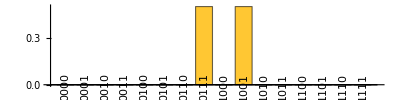

```mathematica
N[QuantumCircuitOperator[{ψInputSuperposition,"Fourier"[4],"PhaseNumber"[3,4,False],"InverseFourier"[4]}]][]["ProbabilitiesPlot",]
```

Show that for the result 0111 the integer is given by 4+3:

```mathematica
FromDigits["0111",2]
```

7

Show that for the result 1001 the integer is given by 6+3:

```mathematica
FromDigits["1001",2]
```

9

## Arbitrary Addition

While a circuit that can add superpositions of numbers to a specific number is already useful for quantum parallelization, you might instead be interested to have a circuit with fixed gates which can add any numbers between 0 and 2^n. This can be implemented as follows:

```mathematica
ClearAll[adderBlock]
adderBlock[n_Integer/;n>0]:=
QuantumCircuitOperator[
Table["C"[Table["PhaseShift"[1+a-b]->2n+1-b,{b,a}],{a}],{a,n}],
"Σ"
]
```

The effect of adderBlock[n] is as follows: given two n-qubit registers (2n wires), it applies a cascade of controlled phase rotations from the addend register onto the accumulator, assuming the accumulator is in the Fourier basis. In that basis, the block adds the addend into the accumulator modulo 2^n while leaving the addend unchanged: ab̃->aOverTilde[(a+b) mod 2] with ∼ denoting “QFT of” . Let’s consider a concrete example:

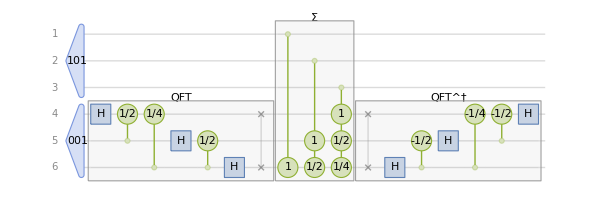

```mathematica
qc1=With[{n=3},
QuantumCircuitOperator[{
"101"->Range[n],
"001"->Range[n+1,2 n],
"Fourier"[3]->Range[n+1,2 n],
adderBlock[3],
"InverseFourier"[n]->Range[n+1,2 n]
}]];
qc1["Diagram",ImageSize->600,Expand->2]
```

Let’s walk through the above circuit step-by-step: Initialize the first three wires in 101 and the last three in 001. Apply QFT to the last three (to move them to the Fourier basis), use the phase adder to add in the Fourier basis, then apply the inverse QFT to return them to the computational basis.

With probability 1, the measured outcome of this circuit gives the state corresponding to 4 when the input states both correspond to 2.

```mathematica
qc1[]["Formula"]
```

101110

Note the first three bits, 101, are the original input, and then last three bits, 110, are the outcome of addition.

Recall the binAdd function from the first lecture; we can use it to verify the result.

```mathematica
binAdd["101","001"]
```

110

## Circuits for Multiplication

Multiplication can be achieved through repeated addition. When multiplying two numbers representable with n bits, the result can always be represented with 2n bits. Since you are now working with a larger register, you can be more efficient with gates by introducing a circuit element that has the effect of adding not just an input, but adding 2^k times that input.

You could define such a circuit element as follows:

```mathematica
ClearAll[kAdderBlock]
kAdderBlock[n_Integer,Optional[k_Integer,0]]/;n>0&&n>=k>=0:=
QuantumCircuitOperator[
Table["C"[Table["PhaseShift"[1+n+a-b-k]->3n+1-b,{b,a+n-k}],{a}],{a,n}],
StringTemplate["2^(`k`)Σ"][<|"k"->k|>]]
```

Let’s construct a circuit to add 2+4×3. First, find the bit-string of 3 in 3-qubit and 2 in 6-qubit:

```mathematica
{3->IntegerString[3,2,3],2->IntegerString[2,2,6]}
```

{3→011,2→000010}

Initialize the circuit with above states, and add 3 four times to 2:

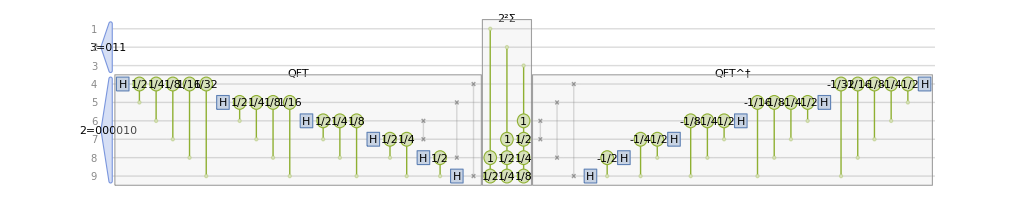

```mathematica
qc2=QuantumCircuitOperator[{
("011"->"Label"->"3=011")->{1,2,3},
("000010"->"Label"->"2=000010")->{4,5,6,7,8,9},
"Fourier"[6]->{4,5,6,7,8,9},
kAdderBlock[3,2],
"InverseFourier"[6]->{4,5,6,7,8,9}
}];
qc2["Diagram",ImageSize->800,Expand->2]
```

In this circuit, 3 is encoded on 3 qubits and 2 on 6 qubits. Apply QFT to the 6-qubit register to move it to the Fourier basis, add the 3 value to it four times in that basis, then apply the inverse QFT to return the result to the computational basis.

As expected, 2+4×3=14, represented in binary form (the first three bits are the original input 010, and the rest, 001010, is the outcome):

```mathematica
Chop[N[qc2][]]["Formula"]
```

1.011001110

which should be read as 011001110 with the 2nd part is the result of the multiplication. The final result 001110 is what we expected for the base-2 form of 14:

```mathematica
FromDigits["001110",2]
```

14

A generic multiplication circuit would then use the following blocks, controlled by bits from another register. A possible implementation looks like this:

```mathematica
ClearAll[mulBlock]
mulBlock[n_Integer]/;n>0:=
QuantumCircuitOperator[
Flatten@Table["C"[Table["PhaseShift"[1+i1+i2-r]->4n+1-r,{r,i1+i2}],{i1,i2+n}],{i1,n},{i2,n}],
"Π"]
```

The above circuit does the multiplication block as a summation.

```mathematica
ClearAll[qftMul]
qftMul[n_Integer]/;n>0:=
QuantumCircuitOperator[{
"Fourier"[2n]->Range[2n+1,4n],
mulBlock[n],
"InverseFourier"[2n]->Range[2n+1,4n]
}]
```

The above circuit combines QFT and inverse QFT blocks with the multiplication subroutine in the Fourier basis.

As a specific example, let’s consider a circuit that multiplies 3×4. Since 4 needs at least 3-qubit, we shall encode both 3 and 4 in 3-qubit.

```mathematica
{3->IntegerString[3,2,3],4->IntegerString[4,2,3]}
```

{3→011,4→100}

Create the multiplication circuit:

```mathematica
qc3=QuantumCircuitOperator[{
"011"->{1,2,3},
"100"->{4,5,6},
QuantumCircuitOperator[qftMul[3],"ShowLabel"->False]
}];
```

Show the circuit diagram:

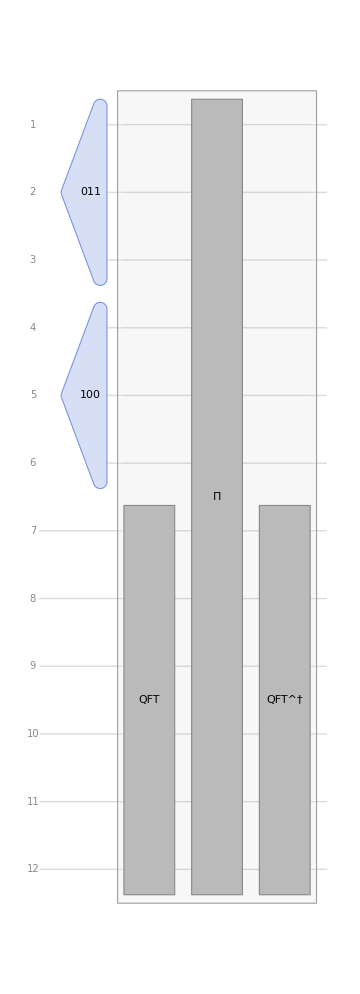

```mathematica
qc3["Diagram"]
```

Show the expanded diagram up to the level 2:

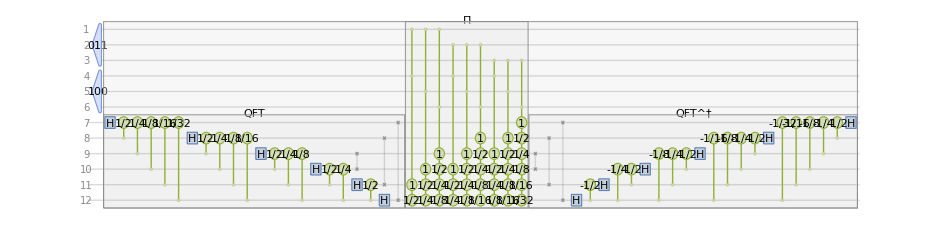

```mathematica
qc3["Diagram","Expand"->2]
```

As expected, you get 9 with 100% probability when running this circuit:

```mathematica
Chop[N[qc3][]]["Formula"]
```

1.011100001100

Read the above result as 011100001100

001100 bit-string corresponds to 12:

```mathematica
FromDigits["001100",2]
```

12

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

Define binAdd function:

```mathematica
binAdd[str1_String,str2_String]/;AllTrue[{str1,str2},StringFreeQ[Except["0"|"1"]..]]:=IntegerString[FromDigits[str1,2]+FromDigits[str2,2],2]
```